# Chapter 5-CIRCULAR MOTION—GRAVITATION

Peter Burbery

Abstract

## Section

XXXX:

## 5-1 to 5-3 Uniform Circular Motion

### 1. (I) A child sitting 1.20 m from the center of a merry-go-round moves with a speed of 1.10 m·s^-1. Calculate {a} the centripetal acceleration of the child and {b} the net horizontal force exerted on the child (mass=22.5 kg).

View possible formulas for centripetal acceleration:

```mathematica
AssociationMap[FormulaData][FormulaLookup["CentripetalAcceleration"]]
```

<|{CentripetalAcceleration,RotationSpeed}→a Acceleration==(v Speed)^2/(r Radius),{CentripetalAcceleration,AngularVelocity}→a Acceleration==r Radius (ω AngularVelocity)^2,{CentripetalAcceleration,AngularVelocity,Diameter}→a Acceleration==1/2 d Diameter (ω AngularVelocity)^2,{CentripetalAcceleration,AngularVelocity,OrbitDistance}→a Acceleration==(ω AngularVelocity)^2 d_o Distance,{CentripetalAcceleration,OrbitSpeed}→a Acceleration==(v Speed)^2/(d_o Distance),{CentripetalAcceleration,OrbitSpeed,Diameter}→a Acceleration==(2 (v Speed)^2)/(d Diameter),{CentripetalAcceleration,OrbitSpeed,Radius}→a Acceleration==(v Speed)^2/(r Radius),{CentripetalAcceleration,RotationRate}→a Acceleration==(4 π^2 /rev^2) (n RevolutionRate)^2 r Radius,{CentripetalAcceleration,RotationRate,Diameter}→a Acceleration==(2 π^2 /rev^2) d Diameter (n RevolutionRate)^2,{CentripetalAcceleration,RotationRate,OrbitDistance}→a Acceleration==(4 π^2 /rev^2) (n RevolutionRate)^2 d_o Distance,{CentripetalAcceleration,RotationSpeed,Diameter}→a Acceleration==(2 (v Speed)^2)/(d Diameter),{CentripetalAcceleration,RotationSpeed,OrbitDistance}→a Acceleration==(v Speed)^2/(d_o Distance)|>

I will use the formula CentripetalAcceleration with RotationSpeed.

Get data for the formula:

```mathematica
FormulaData[{"CentripetalAcceleration", "RotationSpeed"}]
```

a Acceleration==(v Speed)^2/(r Radius)

The table has lots of helpful information:

```mathematica
FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
a | centripetal acceleration | Acceleration | {{LengthUnit,1},{TimeUnit,-2}}
r | radius | Radius | {LengthUnit,1}
v | tangential speed | Speed | {{LengthUnit,1},{TimeUnit,-1}}

#### Formula Classes

I wonder what classes this formula is in.

```mathematica
FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"Classes"]
```

{Physics,{Physics,Mechanics}}

I wonder what other formulas are in the classes:

Make a word cloud for each class:

```mathematica
PersistResourceFunction["FromCamelCase"]
```

Success[…]

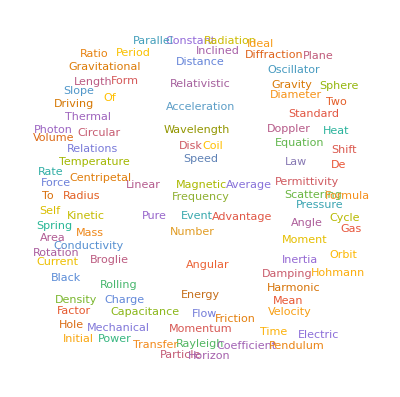

```mathematica
WordCloud[Flatten[TextWords[FromCamelCase[#]]&/@Flatten[FormulaLookup["Physics"]]]]
```

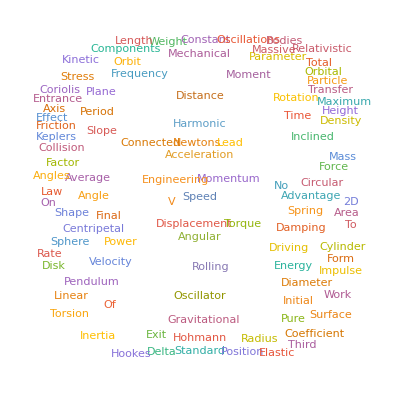

```mathematica
WordCloud[Flatten[TextWords[FromCamelCase[#]]&/@Flatten[FormulaLookup[{"Physics","Mechanics"}]]]]
```

#### using the formula for part a

The child is sitting 1.20m from the merry-go-round so the radius is 1.20m. The speed or velocity is 1.10 m·s^-1.

```mathematica
FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"QuantityVariables"]
```

{a Acceleration,r Radius,v Speed}

I just need the rest of the variables, not a:

```mathematica
Rest[FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"QuantityVariables"]]
```

{r Radius,v Speed}

```mathematica
substitutionRules=AssociationThread[Rest[FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"QuantityVariables"]]->{Quantity[1.2, "Meters"],Quantity[1.1, ("Meters")/("Seconds")]}]
```

<|r Radius→1.2 m,v Speed→1.1 m/s|>

```mathematica
FormulaData[{"CentripetalAcceleration","RotationSpeed"}]/.substitutionRules
```

a Acceleration==1.00833 m/s^2

I'm curious what a rationalized form of this is.

```mathematica
Rationalize[FormulaData[{"CentripetalAcceleration","RotationSpeed"}]/.substitutionRules]
```

a Acceleration==121/120 m/s^2

#### part b

```mathematica
substitutionRules//=AppendTo[First[]]
```

```mathematica
FormulaLookup["CentripetalForce"]
```

{{CentripetalForce,RotationSpeed},{CentripetalForce,AngularVelocity}}

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"}]
```

F Force==(m Mass (v Speed)^2)/(r Radius)

```mathematica
Rest[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]
```

{m Mass,r Radius,v Speed}

```mathematica
substitutionRules=AssociationThread[Rest[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]->Prepend[(Quantity[22.5, "Kilograms"])][Values[substitutionRules]]]
```

<|m Mass→22.5 kg,r Radius→1.2 m,v Speed→1.1 m/s|>

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"}]/.substitutionRules
```

F Force==22.6875 kg m/s^2

```mathematica
Rationalize[FormulaData[{"CentripetalForce","RotationSpeed"}]/.substitutionRules]
```

F Force==363/16 kg m/s^2

#### Notes

I reworded the question.

The original question was

A child sitting 1.20 m from the center of a merry-go-round moves with a speed of 1.10 m/s. Calculate (a) the centripetal acceleration of the child and (b) the net horizontal force exerted on the child (mass=22.5 kg).

I think scientific notation is universally better to use than the oblique stroke / for division. For example  1.10 m·s^-1, written in scientific notation, and 1.10 m/s, written with the oblique stroke for division, are equivalent. However, I would like to mention that scientific notation requires less parentheses and often leads to less confusion. Scientific notation is a powerful way to cover complicated cases whereas division is not. For example, here are several things scientific notation can do that you can't do very well with the / marker or not at all.

The zeroeth exponent. m^0. This has the value 1 except for when you have 0^0. I guess you could write m/m, but I think m^0 is easier to understand.

The plus one exponent. For example m^1 has the value 1.

```mathematica
0^0
```

Indeterminate

```mathematica
100^(2^-1)
```

10

```mathematica
100^(2^-1)
```

10

```mathematica
a^(b^-c)
```

a^(b^-c)

```mathematica
a^(b^-c)===a^(b^-c)
```

True

```mathematica
a^(b^(-c^-d))==a^(b^(-c^-d))
```

True

I wrote down some more of my thoughts on the benefits of this. The files were too large but I made them available in a Google Photos link.

I wrote down some more of my thoughts on the benefits of this at https://photos.app.goo.gl/yWMGanjf6bZ7AMh58 and https://photos.app.goo.gl/dPKd678dtDfkTd3n6.

This is from the quaternion page on wikipedia:

### 3. (I) A horizontal force of 310 N is exerted on a 2.0-kg ball as it rotates (at arm's length) uniformly in a horizontal circle of radius 900 mm. Calculate the speed of the ball.

#### Initial work

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"}]
```

F Force==(m Mass (v Speed)^2)/(r Radius)

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
F | centripetal force | Force | {{LengthUnit,1},{MassUnit,1},{TimeUnit,-2}}
m | mass | Mass | {MassUnit,1}
r | radius | Radius | {LengthUnit,1}
v | tangential speed | Speed | {{LengthUnit,1},{TimeUnit,-1}}

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed"]
```

{{v Speed→-(√(F Force) √(r Radius))/(√(m Mass))},{v Speed→(√(F Force) √(r Radius))/(√(m Mass))}}

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",]
```

{{v Speed→ConditionalExpression[√((F Force r Radius)/(m Mass)), F Force>0&&m Mass>0&&r Radius>0]}}

```mathematica
#>0&/@FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]
```

{F Force>0,m Mass>0,r Radius>0,v Speed>0}

```mathematica
Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]
```

F Force>0&&m Mass>0&&r Radius>0

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",,Assumptions->Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]]
```

{{v Speed→√((F Force r Radius)/(m Mass))}}

```mathematica
substitutionRules=AssociationThread[{"F" "Force","r" "Radius","m" "Mass"}->{Quantity[310, "Newtons"],Quantity[900, "Millimeters"],Quantity[2., "Kilograms"]}]
```

<|F Force→310 N,r Radius→900 mm,m Mass→2. kg|>

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",,Assumptions->Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]]/.substitutionRules
```

{{v Speed→373.497 √mm √N/√kg}}

```mathematica
UnitSimplify[Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",,Assumptions->Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]]/.substitutionRules]
```

{{v Speed→11.811 m/s}}

```mathematica
Rationalize[UnitSimplify[Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",,Assumptions->Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]]/.substitutionRules]]
```

{{v Speed→11.811 m/s}}

#### Notes and comments

I reworded this problem slightly to use millimeters in place of millimeters to be in accordance with NIST SP 811 Chapter 7 Section 9 Choosing SI Prefixes. The original wording was

A horizontal force of 310 N is exerted on a 2.0-kg ball as it rotates (at arm’s length) uniformly in a horizontal circle of radius 0.90 m. Calculate the speed of the ball.

There is a discrepancy here in that when I say 900 mm I have three significant figures but 0.90 m has only two significant figures. I changed this to 900 mm even though there was a discrepancy because it realistic to measure something to nearest millimeter instead of to the nearest centimeter, which is the practice in metric architecture and CAD where all dimensions are in millimeters. If this discrepancy is to be avoided, the problem should solved with something like 9.0E2 mm. If 3 significant figures were known, as is the case for 900 mm, I would write 9.00E2 mm.

There is one other thing with this that I think should be changed which instead of saying a 2.0-kg ball, something like a ball of mass 2.0 kg is better. This is explained in NIST SP 811 Chapter 7 Section 2 Space between numerical value and unit symbol.

In summary, I would revise the question to something like this:

A horizontal force of 310 N is exerted on a ball of mass 2.0 kg as it rotates (at arm’s length) uniformly in a horizontal circle of radius 900 mm. Calculate the speed of the ball.

### 5. (II) A 0.55-kg ball, attached to the end of a horizontal cord, is revolved in a circle of radius 1.3 m on a frictionless horizontal surface. If the cord will break when the tension in it exceeds 75 N, what is the maximum speed the ball can have?

I will reword this to:

A ball of mass 550g, attached to the end of a horizontal cord, is revolved in a circle of radius 1.3 m on a frictionless horizontal surface. If the cord will break when the tension in it exceeds 75 N, what is the maximum speed the ball can have?

```mathematica
substitutionRules=AssociationThread[{"m" "Mass","r" "Radius","F" "Force"}->{Quantity[550, "Grams"],Quantity[1.3, "Meters"],Quantity[75, "Newtons"]}]
```

<|m Mass→550 g,r Radius→1.3 m,F Force→75 N|>

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules
```

75 N==(423.077 g/m) (v Speed)^2

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",]
```

{{v Speed→13.3144 m/s}}

```mathematica
Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-12]
```

{v Velocity==4608866/346157 m/s}

```mathematica
N[Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-12]]
```

{v Velocity==13.3144 m/s}

```mathematica
Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-18]
```

{v Velocity==436898813/32814055 m/s}

```mathematica
N[Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-18]]
```

{v Velocity==13.3144 m/s}

### 7-Graphics-

```mathematica
Solve[m v^2 r^-1==m g,v]
```

{{v→-√g √r},{v→√g √r}}

```mathematica
Solve[m v^2 r^-1==m g,v,]
```

{{v→ConditionalExpression[√(g r), r>0&&m>0&&g>0]}}

```mathematica
FullForm[Solve[m v^2 r^-1==m g,v,]]
```

List[List[Rule[v,ConditionalExpression[Power[Times[g,r],Rational[1,2]],And[Greater[r,0],Greater[m,0],Greater[g,0]]]]]]

```mathematica
First[Solve[m v^2 r^-1==m g,v,]]
```

{v→ConditionalExpression[√(g r), r>0&&m>0&&g>0]}

```mathematica
Last[First[Solve[m v^2 r^-1==m g,v,]]]
```

v→ConditionalExpression[√(g r), r>0&&m>0&&g>0]

```mathematica
Last[Last[First[Solve[m v^2 r^-1==m g,v,]]]]
```

ConditionalExpression[√(g r), r>0&&m>0&&g>0]

```mathematica
Last[Last[Last[First[Solve[m v^2 r^-1==m g,v,]]]]]
```

r>0&&m>0&&g>0

```mathematica
Solve[m v^2 r^-1==m g,v,,Assumptions->{Last[Last[Last[First[Solve[m v^2 r^-1==m g,v,]]]]]}]
```

{{v→√(g r)}}

```mathematica
√(GeogravityModelData["Magnitude"] Quantity[115, "Meters"])
```

33.57 m/s

```mathematica
QuantityForm[√(GeogravityModelData["Magnitude"] Quantity[115, "Meters"]),"Abbreviation"]
```

33.57 m/s

The answer is 33.5699958071 m s^-1.

### 9-Graphics-

```mathematica
eqn= m v^2/r==m g μ
```

(m v^2)/r==g m μ

```mathematica
r>0&&m>0&&g>0
```

r>0&&m>0&&g>0

```mathematica
#>0&/@{r,m,g}
```

{r>0,m>0,g>0}

```mathematica
Apply[And][#>0&/@{r,m,g}]
```

r>0&&m>0&&g>0

```mathematica
Solve[eqn,v]
```

{{v→-√g √r √μ},{v→√g √r √μ}}

```mathematica
Solve[eqn,v,]
```

{{v→ConditionalExpression[√(g r μ), μ>0&&r>0&&m>0&&g>0]}}

```mathematica
Solve[eqn,v,,Assumptions->Apply[And][#>0&/@{r,m,g,μ}]]
```

{{v→√(g r μ)}}

```mathematica
√(GeogravityModelData["Magnitude"](Quantity[90., "Meters"])0.65)
```

23.9431 m/s

```mathematica
CopyToClipboard[QuantityForm[√(GeogravityModelData["Magnitude"](Quantity[90., "Meters"])0.65),"Abbreviation"]]
```

The answer is 23.9431 "m" s^-1".

### 11-Graphics-

```mathematica
eqn=m g -m v^2/r==0
```

g m-(m v^2)/r==0

```mathematica
periodEquation=v==distance/time
```

v==distance/time

```mathematica
distanceEquation=distance==2Pi radius
```

distance==2 π radius

```mathematica
radiusEquation= diameter==2radius
```

diameter==2 radius

```mathematica
Apply[And][{eqn,periodEquation,distanceEquation,radiusEquation}]
```

g m-(m v^2)/r==0&&v==distance/time&&distance==2 π radius&&diameter==2 radius

```mathematica
eqn/.<|v->distance/time|>
```

g m-(distance^2 m)/(r time^2)==0

```mathematica
eqn/.<|v->distance/time|>/.<|distance->2 diameter|>
```

g m-(4 diameter^2 m)/(r time^2)==0

```mathematica
assumeConditionalExpression//ClearAll
assumeConditionalExpression[equation_,variable_,domain_]:=Last[Last[Last[First[Solve[equation,variable,domain]]]]]
```

```mathematica
assumeConditionalExpression[eqn/.<|v->distance/time|>/.<|distance->2 diameter|>,time,]
```

r>0&&m>0&&g>0&&diameter>0

```mathematica
Last[Last[Last[First[Solve[eqn/.<|v->distance/time|>/.<|distance->2 diameter|>,time,]]]]]
```

r>0&&m>0&&g>0&&diameter>0

```mathematica
substitutedEqn=eqn/.<|v->distance/time|>/.<|distance->2 diameter,r->radius,radius->diameter/2|>/.<|radius->diameter/2|>
```

g m-(8 diameter m)/time^2==0

```mathematica
assumeConditionalExpression[substitutedEqn,time,]
```

m>0&&g>0&&diameter>0

```mathematica
Solve[substitutedEqn,time,]
```

{{time→ConditionalExpression[2 √2 √(diameter/g), m>0&&g>0&&diameter>0]}}

```mathematica
Solve[substitutedEqn,time,,Assumptions->{assumeConditionalExpression[substitutedEqn,time,]}]
```

{{time→2 √2 √(diameter/g)}}

```mathematica
solvedEquation=time==2 √2 √(diameter/g)
```

time==2 √2 √(diameter/g)

```mathematica
solvedEquation/.<|diameter->Quantity[25, "Meters"],g->GeogravityModelData["Magnitude"]|>
```

time==4.51765 s

```mathematica
Quantity[1, "Minutes"]/time/.<|time->Last[solvedEquation/.<|diameter->Quantity[25, "Meters"],g->GeogravityModelData["Magnitude"]|>]|>
```

13.2812

```mathematica
Solve[m g ==m v^2/r,v]
```

{{v→-√g √r},{v→√g √r}}

```mathematica
Solve[m g ==m v^2/r,v,]
```

{{v→ConditionalExpression[√(g r), r>0&&m>0&&g>0]}}

```mathematica
Solve[Pi diameter/(time rotation^-1)==√(g radius),time]
```

{{time→(diameter π rotation)/(√(g radius))}}

```mathematica
Solve[Pi diameter/(time rotation^-1)==√(g diameter/2),time]
```

{{time→(√2 diameter π rotation)/(√(diameter g))}}

```mathematica
√2 diameter Pi/(√(diameter g))/.<|diameter->Quantity[25, "Meters"],g->GeogravityModelData["Magnitude"]|>
```

7.09631 s

```mathematica
Quantity[1, "Minutes"]/(√2 diameter Pi/(√(diameter g))/.<|diameter->Quantity[25, "Meters"],g->GeogravityModelData["Magnitude"]|>)
```

8.4551

```mathematica
Round[Quantity[1, "Minutes"]/(√2 diameter Pi/(√(diameter g))/.<|diameter->Quantity[25, "Meters"],g->GeogravityModelData["Magnitude"]|>)]
```

8

```mathematica
Round[Quantity[1, "Minutes"]/(√2 diameter Pi/(√(diameter g))/.<|diameter->Quantity[25, "Meters"],g->GeogravityModelData["Magnitude"]|>),0.1]
```

8.5

### 13-Graphics-

```mathematica
Quantity[1, "Days"]/(√2 diameter Pi/(√(diameter g))/.<|diameter->Quantity[1.1, "Kilometers"],g->0.9GeogravityModelData["Magnitude"]|>)
```

1741.31

```mathematica
Round[Quantity[1, "Days"]/(√2 diameter Pi/(√(diameter g))/.<|diameter->Quantity[1.1, "Kilometers"],g->0.9GeogravityModelData["Magnitude"]|>),0.1]
```

1741.3

```mathematica
Round[Quantity[1, "Days"]/(√2 diameter Pi/(√(diameter g))/.<|diameter->Quantity[1.1, "Kilometers"],g->0.9GeogravityModelData["Magnitude"]|>),1*^2]
```

1700

### 15-Graphics-

```mathematica
Solve[m v^2/r==m g μ,μ]
```

{{μ→v^2/(g r)}}

```mathematica
FormulaData[{"AngularToLinearVelocity","RotationRate","Radius"},"QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
v | linear velocity | LinearSpeed | {{LengthUnit,1},{TimeUnit,-1}}
n | rotation rate | RevolutionRate | {TimeUnit,-1}
r | radius | Radius | {LengthUnit,1}

I have an error so I am going to add Quiet to stop the error from occurring.FormulaData::pq: "The input for n has incorrect units for RevolutionRate." Actually I just turned the message off.

I can enter n as a string:

```mathematica
FormulaData[{"AngularToLinearVelocity","RotationRate","Radius"},{"n"->Quantity[38,("Minutes")^-1]}]
```

v LinearSpeed==(76 π per minuteper revolution) r Radius

I can also enter n as a quantity variable:

```mathematica
FormulaData[{"AngularToLinearVelocity","RotationRate","Radius"},"QuantityVariables"]
```

{v LinearSpeed,n RevolutionRate,r Radius}

```mathematica
FormulaData[{"AngularToLinearVelocity","RotationRate","Radius"},{"n" "RevolutionRate"->Quantity[38,("Minutes")^-1]}]
```

v LinearSpeed==(76 π per minuteper revolution) r Radius

Give the radius:

```mathematica
FormulaData[{"AngularToLinearVelocity","RotationRate","Radius"},{"n" "RevolutionRate"->Quantity[38,("Minutes")^-1],"r" "Radius"->Quantity[130, "Millimeters"]}]
```

v LinearSpeed==(247 π)/1500 mm/(ms rev)

```mathematica
Cases[q_?QuantityQ][Level[%,1]]
```

{(247 π)/1500 mm/(ms rev)}

```mathematica
UnitConvert[Cases[q_?QuantityQ][Level[%,1]]]
```

{(247 π)/1500 m/(s rev)}

```mathematica
UnitConvert[Cases[q_?QuantityQ][Level[%,1]]//N]
```

{0.517316 m/(s rev)}

```mathematica
UnitConvert[Cases[q_?QuantityQ][Level[%,1]]//N,"Millimeters"("Minutes")^-1("Revolutions")^-1]
```

{31038.9 mm/(min rev)}

```mathematica
UnitConvert[Cases[q_?QuantityQ][Level[%,1]]//N,"Meters"("Minutes")^-1("Revolutions")^-1]
```

{31.0389 m/(min rev)}

```mathematica
UnitConvert[Cases[q_?QuantityQ][Level[%,1]]//N,"Meters"("Seconds")^-1("Revolutions")^-1]
```

{0.517316 m/(s rev)}

```mathematica
UnitConvert[Cases[q_?QuantityQ][Level[%,1]]//N,"Millimeters"("Seconds")^-1("Revolutions")^-1]
```

{517.316 mm/(s rev)}

```mathematica
Solve[m v^2/r==m g μ,μ]
```

{{μ→v^2/(g r)}}

```mathematica
Solve[m v^2/r==m g μ,μ]/.<|v->First@UnitConvert[Cases[q_?QuantityQ][Level[%39,1]]//N,"Millimeters"("Seconds")^-1("Revolutions")^-1],g->Quantity[, "StandardAccelerationOfGravity"],r->Quantity[130, "Millimeters"]|>
```

{{μ→2058.58 mm/(s^2 rev^2 g)}}

```mathematica
UnitSimplify[Solve[m v^2/r==m g μ,μ]/.<|v->First@UnitConvert[Cases[q_?QuantityQ][Level[%39,1]]//N,"Millimeters"("Seconds")^-1("Revolutions")^-1],g->Quantity[, "StandardAccelerationOfGravity"],r->Quantity[130, "Millimeters"]|>]
```

{{μ→0.209917 /rev^2}}

The book has 0.210 as the answer.

### 17-Graphics-

### 19-Graphics-

```mathematica
FormulaData[{"Weight"}]
```

```mathematica
Quantity[975, "Kilograms"]GeogravityModelData["Magnitude"]
```

9554.53 kg m/s^2

```mathematica
UnitSimplify[Quantity[975, "Kilograms"]GeogravityModelData["Magnitude"]]
```

9.55453 kN

```mathematica
UnitSimplify[Quantity[62.0, "Kilograms"]GeogravityModelData["Magnitude"]]
```

0.60757 kN

```mathematica
UnitConvert[UnitSimplify[Quantity[62.0, "Kilograms"]GeogravityModelData["Magnitude"]],"Newtons"]
```

607.57 N

```mathematica
√(GeogravityModelData["Magnitude"](Quantity[88., "Meters"]))
```

29.3659 m/s

```mathematica
QuantityMagnitude[√(GeogravityModelData["Magnitude"](Quantity[88., "Meters"]))]
```

29.3659

```mathematica
NumberForm[QuantityMagnitude[√(GeogravityModelData["Magnitude"](Quantity[88., "Meters"]))],100,DigitBlock->3]
```

29.365 926 191 879 95

```mathematica
Round[29.365,0.1]
```

29.4

```mathematica
Factor[m g - m v^2 r^-1]
```

(m (g r-v^2))/r

```mathematica
massInNormalForceOut//ClearAll
massInNormalForceOut[mass_?QuantityQ]/;ContainsExactly[{{"MassUnit",1}}][UnitDimensions[mass]]:=mass(GeogravityModelData["Magnitude"] Quantity[88., "Meters"]-Quantity[18, ("Meters")/("Seconds")]^2)/Quantity[88., "Meters"]
```

```mathematica
massInNormalForceOut[Quantity[975, "Kilograms"]]
```

5964.76 kg m/s^2

```mathematica
UnitConvert[massInNormalForceOut[Quantity[975, "Kilograms"]],"Newtons"]
```

5964.76 N

```mathematica
UnitConvert[massInNormalForceOut[Quantity[975, "Kilograms"]],"KiloNewtons"]
```

5.96476 kN

```mathematica
QuantityMagnitude[UnitConvert[massInNormalForceOut[Quantity[975, "Kilograms"]],"KiloNewtons"]]
```

5.96476

```mathematica
FormatNumber//ClearAll
FormatNumber[n_?NumberQ]:=NumberForm[n,100,DigitBlock->3]
FormatNumber[n_?QuantityQ]:=NumberForm[n,100,DigitBlock->3]
```

```mathematica
FormatNumber[%73]
```

5.964 757 733 855 31

```mathematica
Round[UnitConvert[massInNormalForceOut[Quantity[975, "Kilograms"]],"Newtons"],10]
```

5960 N

```mathematica
massInNormalForceOut[Quantity[62, "Kilograms"]]
```

379.297 kg m/s^2

```mathematica
Round[massInNormalForceOut[Quantity[62, "Kilograms"]],1]
```

379 kg m/s^2

```mathematica
UnitConvert[Round[massInNormalForceOut[Quantity[62, "Kilograms"]],1],"Newtons"]
```

379 N

```mathematica
NumberForm[massInNormalForceOut[Quantity[62, "Kilograms"]],100, DigitBlock->3]
```

379.297 414 870 799 2 kg m/s^2

```mathematica
FormatNumber[UnitConvert[massInNormalForceOut[Quantity[62, "Kilograms"]],"Newtons"]]
```

379.297 414 870 799 2 N

### 21-Graphics-

```mathematica
FormulaLookup["Kinematics"]
```

{{ReynoldsNumber,KinematicViscosity},{SchmidtNumber,KinematicViscosity}}

```mathematica
FormulaLookup[{"Physics","Mechanics"}]
```

{ThrowingAngle,EnergyEfficiency,MomentOfInertiaRatio,AngularDiameter,AngularFrequency,{AngularToLinearVelocity,AngularVelocity,Radius},{AngularToLinearVelocity,AngularVelocity,Diameter},{AngularToLinearVelocity,AngularVelocity,OrbitDistance},{AngularToLinearVelocity,Period,Radius},{AngularToLinearVelocity,Period,Diameter},{AngularToLinearVelocity,Period,OrbitDistance},{AngularToLinearVelocity,RotationRate,Radius},{AngularToLinearVelocity,RotationRate,Diameter},{AngularToLinearVelocity,RotationRate,OrbitDistance},AnnulusAreaMomentOfInertia,{AverageAngularVelocity,AngularDisplacement},{AverageAngularVelocity,Angles},{AverageAngularVelocity,Velocities},{AverageAngularVelocity,Velocities,Angles},{AverageSpeed,TotalDistance},{AverageSpeed,Positions},{AverageSpeed,Speeds},{AverageSpeed,Speeds,Positions},Buoyancy,{CentripetalAcceleration,RotationSpeed},{CentripetalAcceleration,AngularVelocity},{CentripetalAcceleration,RotationRate},{CentripetalAcceleration,OrbitSpeed,Radius},{CentripetalAcceleration,RotationSpeed,Diameter},{CentripetalAcceleration,AngularVelocity,Diameter},{CentripetalAcceleration,RotationRate,Diameter},{CentripetalAcceleration,OrbitSpeed,Diameter},{CentripetalAcceleration,RotationSpeed,OrbitDistance},{CentripetalAcceleration,AngularVelocity,OrbitDistance},{CentripetalAcceleration,RotationRate,OrbitDistance},{CentripetalAcceleration,OrbitSpeed},{CentripetalForce,RotationSpeed},{CentripetalForce,AngularVelocity},{CircularOrbitSpeed,OrbitRadius},{CircularOrbitSpeed,Altitude},ConeMomentOfInertia,{CoriolisEffect,Standard},{CoriolisEffect,Force},CuboidMomentOfInertia,{CylinderMechanicalStress,Diameter},{CylinderMechanicalStress,Radius},CylinderMomentOfInertia,{DiskAreaMomentOfInertia,Radius},{DiskAreaMomentOfInertia,Diameter},DiskMomentOfInertia,{DistanceSpeedTime,ConstantSpeed},{DistanceSpeedTime,Acceleration},{DistanceSpeedTime,Acceleration,InitialSpeed},{DistanceSpeedTime,InitialPosition},{DistanceSpeedTime,Acceleration,InitialPosition},{DistanceSpeedTime,Acceleration,InitialSpeed,InitialPosition},{DistanceSpeedTimeCircularForm,ConstantSpeed},{DistanceSpeedTimeCircularForm,InitialAngle},{DistanceSpeedTimeCircularForm,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngularSpeed,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngle,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngle,InitialAngularSpeed,AngularAcceleration},DrivingDistanceSpeedTime,EarthCircularOrbitPeriod,ElasticCollision,{ElasticCollision2D,Radius},{ElasticCollision2D,Angle},EllipticalLaminaMomentOfInertia,EllipticOrbitFormula,{EngineeringStrain,LengthDifference},{EngineeringStrain,Lengths},EscapeVelocity,FluidColumnPressure,ForceComponents,{GravitationalAcceleration,Radius},{GravitationalAcceleration,Radius,Height},GravitationalPotentialEnergy,HalfDiskAreaMomentOfInertia,{HarmonicOscillator,NoInfluences},{HarmonicOscillator,Damping},{HarmonicOscillator,Driving},{HarmonicOscillator,Damping,Driving},{HarmonicOscillator,FrequencyPeriod},{HarmonicOscillator,FrequencyPeriod,Damping},{HarmonicOscillator,FrequencyPeriod,Driving},{HarmonicOscillator,FrequencyPeriod,Damping,Driving},{HarmonicOscillator,Spring},{HarmonicOscillator,Spring,Damping},{HarmonicOscillator,Spring,Driving},{HarmonicOscillator,Spring,Damping,Driving},{HarmonicOscillator,Spring,FrequencyPeriod},{HarmonicOscillator,Spring,FrequencyPeriod,Damping},{HarmonicOscillator,Spring,FrequencyPeriod,Driving},{HarmonicOscillator,Spring,FrequencyPeriod,Damping,Driving},{HarmonicOscillator,Pendulum},{HarmonicOscillator,Pendulum,Damping},{HarmonicOscillator,Pendulum,Driving},{HarmonicOscillator,Pendulum,Damping,Driving},{HarmonicOscillator,Pendulum,FrequencyPeriod},{HarmonicOscillator,Pendulum,FrequencyPeriod,Damping},{HarmonicOscillator,Pendulum,FrequencyPeriod,Driving},{HarmonicOscillator,Pendulum,FrequencyPeriod,Damping,Driving},{HarmonicOscillator,Torsion},{HarmonicOscillator,Torsion,Damping},{HarmonicOscillator,Torsion,Driving},{HarmonicOscillator,Torsion,Damping,Driving},{HarmonicOscillator,Torsion,FrequencyPeriod},{HarmonicOscillator,Torsion,FrequencyPeriod,Driving},{HarmonicOscillator,Torsion,FrequencyPeriod,Damping,Driving},HexagonAreaMomentOfInertia,HohmannAngularAlignment,{HohmannEntranceDeltaV,Mass},{HohmannEntranceDeltaV,GravitationalParameter},{HohmannExitDeltaV,Mass},{HohmannExitDeltaV,GravitationalParameter},{HohmannTotalDeltaV,Mass},{HohmannTotalDeltaV,GravitationalParameter},{HohmannTransferTime,OrbitalRadii,Mass},{HohmannTransferTime,OrbitalRadii,GravitationalParameter},{HohmannTransferTime,SemimajorAxis,Mass},{HohmannTransferTime,SemimajorAxis,GravitationalParameter},HollowCylinderMechanicalStress,{HookesLaw,Force},{HookesLaw,PotentialEnergy},{Impulse,Force},{Impulse,Momentum},{Impulse,Speed},{InclinedPlaneMechanicalAdvantage,LengthHeight},{InclinedPlaneMechanicalAdvantage,Slope},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,SpeedDistance},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,SpeedDistance},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration,SpeedDistance},InclinedSpanSag,KeplersFirstLaw,{KeplersThirdLaw,Sun},{KeplersThirdLaw,SingleMass},{KeplersThirdLaw,Masses},KineticEnergy,KineticEnergyRelativistic,{KineticEnergySphere,Radius},{KineticEnergySphere,Diameter},{KineticEnergySphereRelativistic,Radius},{KineticEnergySphereRelativistic,Diameter},KineticFrictionCoefficient,LevelSpanSag,LeverMechanicalAdvantage,MassDensity,{MechanicalPower,Work,Time},{MechanicalPower,Force,Speed},{MechanicalPower,Force,Speed,Angle},MechanicalStress,MinimumPowerRequiredToMoveObject,NewtonsLawOfUniversalGravitation,NewtonsSecondLawConstantMass,{Momentum,Speed},{Momentum,KineticEnergy},ParallelAxisTheorem,{ParticleCollision,Inelastic},{ParticleCollision,Elastic,CoefficientOfRestitution},{ParticleCollision,Surface},{ParticleCollision,Surface,CoefficientOfRestitution},{Pendulum,Standard},{Pendulum,MomentOfInertia},{PendulumSmallOscillations,Standard},{PendulumSmallOscillations,MomentOfInertia},PentagonAreaMomentOfInertia,PointMassMomentOfInertia,Pressure,Projectile,ProjectileSlantRange,PulleySystemMechanicalAdvantage,QuarterDiskAreaMomentOfInertia,RectangleAreaMomentOfInertia,ReducedMass,RigidBodyAngularMomentum,RocketEquation,Rolling,RollingFrictionCoefficient,RotationalKineticEnergy,RotationalPower,{ScrewMechanicalAdvantage,Lead},{ScrewMechanicalAdvantage,LeadAngle},SolidEllipsoidMomentOfInertia,{SpeedAccelerationDistance,Distance},{SpeedAccelerationDistance,InitialPosition,FinalPosition},{SpeedAccelerationDistanceCircularForm,AngularDisplacement},{SpeedAccelerationDistanceCircularForm,InitialAngle,FinalAngle},{SpeedAccelerationTime,NoInitialSpeed},{SpeedAccelerationTime,InitialSpeed},{SpeedAccelerationTime,DeltaSpeed},{SpeedAccelerationTimeCircularForm,NoInitialAngularSpeed},{SpeedAccelerationTimeCircularForm,InitialAngularSpeed},SphereMomentOfInertia,SpringConstant,SpringMaximumForce,SpringMaximumShearStress,{StaticFrictionCoefficient,FrictionForce},{StaticFrictionCoefficient,CriticalSlidingAngle},ThinRodMomentOfInertia,{Torque,Perpendicular},{Torque,Angle},Torsion,TrapezoidAreaMomentOfInertia,TriangleAreaMomentOfInertia,TriangularPlateMomentOfInertia,{TwoConnectedSprings,Parallel},{TwoConnectedSprings,Serial},UniformDensitySphereGravitationalBindingEnergy,VelocityComponents,{VisViva,Mass},{VisViva,GravitationalParameter},{WedgeMechanicalAdvantage,LengthThickness},{WedgeMechanicalAdvantage,Angle},{Weight,StandardGravitationalAcceleration},{Weight,GravitationalAcceleration},{WeightOnMassiveBodies,Surface},{WeightOnMassiveBodies,Height},WheelAndAxleMechanicalAdvantage,{Work,Standard},{Work,Angle},{Work,Acceleration},{Work,Gravity},{Work,Torque},{MomentumRelativistic,Velocity},{MomentumRelativistic,KineticEnergy}}

```mathematica
?MemberQ
```

```mathematica
Select[MemberQ[FormulaData[#,"Classes"],{"Physics","Mechanics"}]&][FormulaLookup["Acceleration"]]
```

{{CentripetalAcceleration,AngularVelocity},{CentripetalAcceleration,OrbitSpeed},{CentripetalAcceleration,RotationRate},{CentripetalAcceleration,RotationSpeed},{DistanceSpeedTime,Acceleration},{DistanceSpeedTimeCircularForm,AngularAcceleration},{GravitationalAcceleration,Radius},{SpeedAccelerationDistance,Distance},{SpeedAccelerationDistanceCircularForm,AngularDisplacement},{SpeedAccelerationTime,DeltaSpeed},{SpeedAccelerationTime,InitialSpeed},{SpeedAccelerationTime,NoInitialSpeed},{SpeedAccelerationTimeCircularForm,InitialAngularSpeed},{SpeedAccelerationTimeCircularForm,NoInitialAngularSpeed},{Weight,GravitationalAcceleration},{Weight,StandardGravitationalAcceleration},{Work,Acceleration},{CentripetalAcceleration,AngularVelocity,Diameter},{CentripetalAcceleration,AngularVelocity,OrbitDistance},{CentripetalAcceleration,OrbitSpeed,Diameter},{CentripetalAcceleration,OrbitSpeed,Radius},{CentripetalAcceleration,RotationRate,Diameter},{CentripetalAcceleration,RotationRate,OrbitDistance},{CentripetalAcceleration,RotationSpeed,Diameter},{CentripetalAcceleration,RotationSpeed,OrbitDistance},{DistanceSpeedTime,Acceleration,InitialPosition},{DistanceSpeedTime,Acceleration,InitialSpeed},{DistanceSpeedTimeCircularForm,InitialAngle,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngularSpeed,AngularAcceleration},{GravitationalAcceleration,Radius,Height},{SpeedAccelerationDistance,InitialPosition,FinalPosition},{SpeedAccelerationDistanceCircularForm,InitialAngle,FinalAngle},{DistanceSpeedTime,Acceleration,InitialSpeed,InitialPosition},{DistanceSpeedTimeCircularForm,InitialAngle,InitialAngularSpeed,AngularAcceleration},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration,SpeedDistance},{CentripetalAcceleration,AngularVelocity},{CentripetalAcceleration,OrbitSpeed},{CentripetalAcceleration,RotationRate},{CentripetalAcceleration,RotationSpeed},{DistanceSpeedTime,Acceleration},{DistanceSpeedTimeCircularForm,AngularAcceleration},{GravitationalAcceleration,Radius},{SpeedAccelerationDistance,Distance},{SpeedAccelerationDistanceCircularForm,AngularDisplacement},{SpeedAccelerationTime,DeltaSpeed},{SpeedAccelerationTime,InitialSpeed},{SpeedAccelerationTime,NoInitialSpeed},{SpeedAccelerationTimeCircularForm,InitialAngularSpeed},{SpeedAccelerationTimeCircularForm,NoInitialAngularSpeed},{Weight,GravitationalAcceleration},{Weight,StandardGravitationalAcceleration},{Work,Acceleration},{CentripetalAcceleration,AngularVelocity,Diameter},{CentripetalAcceleration,AngularVelocity,OrbitDistance},{CentripetalAcceleration,OrbitSpeed,Diameter},{CentripetalAcceleration,OrbitSpeed,Radius},{CentripetalAcceleration,RotationRate,Diameter},{CentripetalAcceleration,RotationRate,OrbitDistance},{CentripetalAcceleration,RotationSpeed,Diameter},{CentripetalAcceleration,RotationSpeed,OrbitDistance},{DistanceSpeedTime,Acceleration,InitialPosition},{DistanceSpeedTime,Acceleration,InitialSpeed},{DistanceSpeedTimeCircularForm,InitialAngle,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngularSpeed,AngularAcceleration},{GravitationalAcceleration,Radius,Height},{SpeedAccelerationDistance,InitialPosition,FinalPosition},{SpeedAccelerationDistanceCircularForm,InitialAngle,FinalAngle},{DistanceSpeedTime,Acceleration,InitialSpeed,InitialPosition},{DistanceSpeedTimeCircularForm,InitialAngle,InitialAngularSpeed,AngularAcceleration},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration,SpeedDistance}}

```mathematica
GroupBy[First][Select[MemberQ[FormulaData[#,"Classes"],{"Physics","Mechanics"}]&][FormulaLookup["Acceleration"]]]
```

<|CentripetalAcceleration→{{CentripetalAcceleration,AngularVelocity},{CentripetalAcceleration,OrbitSpeed},{CentripetalAcceleration,RotationRate},{CentripetalAcceleration,RotationSpeed},{CentripetalAcceleration,AngularVelocity,Diameter},{CentripetalAcceleration,AngularVelocity,OrbitDistance},{CentripetalAcceleration,OrbitSpeed,Diameter},{CentripetalAcceleration,OrbitSpeed,Radius},{CentripetalAcceleration,RotationRate,Diameter},{CentripetalAcceleration,RotationRate,OrbitDistance},{CentripetalAcceleration,RotationSpeed,Diameter},{CentripetalAcceleration,RotationSpeed,OrbitDistance},{CentripetalAcceleration,AngularVelocity},{CentripetalAcceleration,OrbitSpeed},{CentripetalAcceleration,RotationRate},{CentripetalAcceleration,RotationSpeed},{CentripetalAcceleration,AngularVelocity,Diameter},{CentripetalAcceleration,AngularVelocity,OrbitDistance},{CentripetalAcceleration,OrbitSpeed,Diameter},{CentripetalAcceleration,OrbitSpeed,Radius},{CentripetalAcceleration,RotationRate,Diameter},{CentripetalAcceleration,RotationRate,OrbitDistance},{CentripetalAcceleration,RotationSpeed,Diameter},{CentripetalAcceleration,RotationSpeed,OrbitDistance}},DistanceSpeedTime→{{DistanceSpeedTime,Acceleration},{DistanceSpeedTime,Acceleration,InitialPosition},{DistanceSpeedTime,Acceleration,InitialSpeed},{DistanceSpeedTime,Acceleration,InitialSpeed,InitialPosition},{DistanceSpeedTime,Acceleration},{DistanceSpeedTime,Acceleration,InitialPosition},{DistanceSpeedTime,Acceleration,InitialSpeed},{DistanceSpeedTime,Acceleration,InitialSpeed,InitialPosition}},DistanceSpeedTimeCircularForm→{{DistanceSpeedTimeCircularForm,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngle,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngularSpeed,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngle,InitialAngularSpeed,AngularAcceleration},{DistanceSpeedTimeCircularForm,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngle,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngularSpeed,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngle,InitialAngularSpeed,AngularAcceleration}},GravitationalAcceleration→{{GravitationalAcceleration,Radius},{GravitationalAcceleration,Radius,Height},{GravitationalAcceleration,Radius},{GravitationalAcceleration,Radius,Height}},SpeedAccelerationDistance→{{SpeedAccelerationDistance,Distance},{SpeedAccelerationDistance,InitialPosition,FinalPosition},{SpeedAccelerationDistance,Distance},{SpeedAccelerationDistance,InitialPosition,FinalPosition}},SpeedAccelerationDistanceCircularForm→{{SpeedAccelerationDistanceCircularForm,AngularDisplacement},{SpeedAccelerationDistanceCircularForm,InitialAngle,FinalAngle},{SpeedAccelerationDistanceCircularForm,AngularDisplacement},{SpeedAccelerationDistanceCircularForm,InitialAngle,FinalAngle}},SpeedAccelerationTime→{{SpeedAccelerationTime,DeltaSpeed},{SpeedAccelerationTime,InitialSpeed},{SpeedAccelerationTime,NoInitialSpeed},{SpeedAccelerationTime,DeltaSpeed},{SpeedAccelerationTime,InitialSpeed},{SpeedAccelerationTime,NoInitialSpeed}},SpeedAccelerationTimeCircularForm→{{SpeedAccelerationTimeCircularForm,InitialAngularSpeed},{SpeedAccelerationTimeCircularForm,NoInitialAngularSpeed},{SpeedAccelerationTimeCircularForm,InitialAngularSpeed},{SpeedAccelerationTimeCircularForm,NoInitialAngularSpeed}},Weight→{{Weight,GravitationalAcceleration},{Weight,StandardGravitationalAcceleration},{Weight,GravitationalAcceleration},{Weight,StandardGravitationalAcceleration}},Work→{{Work,Acceleration},{Work,Acceleration}},InclinedPlaneRolling→{{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration,SpeedDistance}}|>

```mathematica
SortBy[Length][GroupBy[First][Select[MemberQ[FormulaData[#,"Classes"],{"Physics","Mechanics"}]&][FormulaLookup["Acceleration"]]]]
```

<|Work→{{Work,Acceleration},{Work,Acceleration}},GravitationalAcceleration→{{GravitationalAcceleration,Radius},{GravitationalAcceleration,Radius,Height},{GravitationalAcceleration,Radius},{GravitationalAcceleration,Radius,Height}},SpeedAccelerationDistance→{{SpeedAccelerationDistance,Distance},{SpeedAccelerationDistance,InitialPosition,FinalPosition},{SpeedAccelerationDistance,Distance},{SpeedAccelerationDistance,InitialPosition,FinalPosition}},SpeedAccelerationDistanceCircularForm→{{SpeedAccelerationDistanceCircularForm,AngularDisplacement},{SpeedAccelerationDistanceCircularForm,InitialAngle,FinalAngle},{SpeedAccelerationDistanceCircularForm,AngularDisplacement},{SpeedAccelerationDistanceCircularForm,InitialAngle,FinalAngle}},SpeedAccelerationTimeCircularForm→{{SpeedAccelerationTimeCircularForm,InitialAngularSpeed},{SpeedAccelerationTimeCircularForm,NoInitialAngularSpeed},{SpeedAccelerationTimeCircularForm,InitialAngularSpeed},{SpeedAccelerationTimeCircularForm,NoInitialAngularSpeed}},Weight→{{Weight,GravitationalAcceleration},{Weight,StandardGravitationalAcceleration},{Weight,GravitationalAcceleration},{Weight,StandardGravitationalAcceleration}},SpeedAccelerationTime→{{SpeedAccelerationTime,DeltaSpeed},{SpeedAccelerationTime,InitialSpeed},{SpeedAccelerationTime,NoInitialSpeed},{SpeedAccelerationTime,DeltaSpeed},{SpeedAccelerationTime,InitialSpeed},{SpeedAccelerationTime,NoInitialSpeed}},DistanceSpeedTime→{{DistanceSpeedTime,Acceleration},{DistanceSpeedTime,Acceleration,InitialPosition},{DistanceSpeedTime,Acceleration,InitialSpeed},{DistanceSpeedTime,Acceleration,InitialSpeed,InitialPosition},{DistanceSpeedTime,Acceleration},{DistanceSpeedTime,Acceleration,InitialPosition},{DistanceSpeedTime,Acceleration,InitialSpeed},{DistanceSpeedTime,Acceleration,InitialSpeed,InitialPosition}},DistanceSpeedTimeCircularForm→{{DistanceSpeedTimeCircularForm,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngle,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngularSpeed,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngle,InitialAngularSpeed,AngularAcceleration},{DistanceSpeedTimeCircularForm,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngle,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngularSpeed,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngle,InitialAngularSpeed,AngularAcceleration}},InclinedPlaneRolling→{{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration,SpeedDistance}},CentripetalAcceleration→{{CentripetalAcceleration,AngularVelocity},{CentripetalAcceleration,OrbitSpeed},{CentripetalAcceleration,RotationRate},{CentripetalAcceleration,RotationSpeed},{CentripetalAcceleration,AngularVelocity,Diameter},{CentripetalAcceleration,AngularVelocity,OrbitDistance},{CentripetalAcceleration,OrbitSpeed,Diameter},{CentripetalAcceleration,OrbitSpeed,Radius},{CentripetalAcceleration,RotationRate,Diameter},{CentripetalAcceleration,RotationRate,OrbitDistance},{CentripetalAcceleration,RotationSpeed,Diameter},{CentripetalAcceleration,RotationSpeed,OrbitDistance},{CentripetalAcceleration,AngularVelocity},{CentripetalAcceleration,OrbitSpeed},{CentripetalAcceleration,RotationRate},{CentripetalAcceleration,RotationSpeed},{CentripetalAcceleration,AngularVelocity,Diameter},{CentripetalAcceleration,AngularVelocity,OrbitDistance},{CentripetalAcceleration,OrbitSpeed,Diameter},{CentripetalAcceleration,OrbitSpeed,Radius},{CentripetalAcceleration,RotationRate,Diameter},{CentripetalAcceleration,RotationRate,OrbitDistance},{CentripetalAcceleration,RotationSpeed,Diameter},{CentripetalAcceleration,RotationSpeed,OrbitDistance}}|>

```mathematica
Keys[SortBy[Length][GroupBy[First][Select[MemberQ[FormulaData[#,"Classes"],{"Physics","Mechanics"}]&][FormulaLookup["Acceleration"]]]]]
```

{Work,GravitationalAcceleration,SpeedAccelerationDistance,SpeedAccelerationDistanceCircularForm,SpeedAccelerationTimeCircularForm,Weight,SpeedAccelerationTime,DistanceSpeedTime,DistanceSpeedTimeCircularForm,InclinedPlaneRolling,CentripetalAcceleration}

```mathematica
?StringContainsQ
```

```mathematica
Select[StringContainsQ["acceleration",IgnoreCase->True]][Keys[SortBy[Length][GroupBy[First][Select[MemberQ[FormulaData[#,"Classes"],{"Physics","Mechanics"}]&][FormulaLookup["Acceleration"]]]]]]
```

{GravitationalAcceleration,SpeedAccelerationDistance,SpeedAccelerationDistanceCircularForm,SpeedAccelerationTimeCircularForm,SpeedAccelerationTime,CentripetalAcceleration}

```mathematica
groupedByFirst=GroupBy[First][Select[MemberQ[FormulaData[#,"Classes"],{"Physics","Mechanics"}]&][FormulaLookup["Acceleration"]]];
```

```mathematica
Select[StringContainsQ["acceleration",IgnoreCase->True]][Keys[SortBy[Length][groupedByFirst]]]
```

{GravitationalAcceleration,SpeedAccelerationDistance,SpeedAccelerationDistanceCircularForm,SpeedAccelerationTimeCircularForm,SpeedAccelerationTime,CentripetalAcceleration}

```mathematica
?Lookup
```

```mathematica
AssociationMap[AssociationMap[FormulaData][Lookup[groupedByFirst,#]]&][Select[StringContainsQ["acceleration",IgnoreCase->True]][Keys[SortBy[Length][groupedByFirst]]]]
```

<|GravitationalAcceleration→<|{GravitationalAcceleration,Radius}→g GravitationalAcceleration==(( G) M Mass)/(r Radius)^2,{GravitationalAcceleration,Radius,Height}→g GravitationalAcceleration==(Piecewise[{{(( G) M Mass)/(h Height+r Radius)^2, h Height≥0}, {(( G) M Mass (h Height+r Radius))/(r Radius)^3, -r Radius≤h Height<0}, {0, True}}])|>,SpeedAccelerationDistance→<|{SpeedAccelerationDistance,Distance}→(v_f Speed)^2==2 a Acceleration d Distance+(v_i Speed)^2,{SpeedAccelerationDistance,InitialPosition,FinalPosition}→(v_f Speed)^2==(v_i Speed)^2+2 a Acceleration (x_f Length-x_i Length)|>,SpeedAccelerationDistanceCircularForm→<|{SpeedAccelerationDistanceCircularForm,AngularDisplacement}→(ω_f AngularVelocity)^2==2 α AngularAcceleration θ Angle+(ω_i AngularVelocity)^2,{SpeedAccelerationDistanceCircularForm,InitialAngle,FinalAngle}→(ω_f AngularVelocity)^2==2 α AngularAcceleration (θ_f Angle-θ_i Angle)+(ω_i AngularVelocity)^2|>,SpeedAccelerationTimeCircularForm→<|{SpeedAccelerationTimeCircularForm,InitialAngularSpeed}→ω_f AngularVelocity==t Time α AngularAcceleration+ω_i AngularVelocity,{SpeedAccelerationTimeCircularForm,NoInitialAngularSpeed}→ω AngularVelocity==t Time α AngularAcceleration|>,SpeedAccelerationTime→<|{SpeedAccelerationTime,DeltaSpeed}→Δv Speed==a Acceleration t Time,{SpeedAccelerationTime,InitialSpeed}→v_f Speed==a Acceleration t Time+v_i Speed,{SpeedAccelerationTime,NoInitialSpeed}→v Speed==a Acceleration t Time|>,CentripetalAcceleration→<|{CentripetalAcceleration,AngularVelocity}→a Acceleration==r Radius (ω AngularVelocity)^2,{CentripetalAcceleration,OrbitSpeed}→a Acceleration==(v Speed)^2/(d_o Distance),{CentripetalAcceleration,RotationRate}→a Acceleration==(4 π^2 /rev^2) (n RevolutionRate)^2 r Radius,{CentripetalAcceleration,RotationSpeed}→a Acceleration==(v Speed)^2/(r Radius),{CentripetalAcceleration,AngularVelocity,Diameter}→a Acceleration==1/2 d Diameter (ω AngularVelocity)^2,{CentripetalAcceleration,AngularVelocity,OrbitDistance}→a Acceleration==(ω AngularVelocity)^2 d_o Distance,{CentripetalAcceleration,OrbitSpeed,Diameter}→a Acceleration==(2 (v Speed)^2)/(d Diameter),{CentripetalAcceleration,OrbitSpeed,Radius}→a Acceleration==(v Speed)^2/(r Radius),{CentripetalAcceleration,RotationRate,Diameter}→a Acceleration==(2 π^2 /rev^2) d Diameter (n RevolutionRate)^2,{CentripetalAcceleration,RotationRate,OrbitDistance}→a Acceleration==(4 π^2 /rev^2) (n RevolutionRate)^2 d_o Distance,{CentripetalAcceleration,RotationSpeed,Diameter}→a Acceleration==(2 (v Speed)^2)/(d Diameter),{CentripetalAcceleration,RotationSpeed,OrbitDistance}→a Acceleration==(v Speed)^2/(d_o Distance)|>|>

```mathematica
FormulaData[{"SpeedAccelerationDistance","Distance"}]
```

(v_f Speed)^2==2 a Acceleration d Distance+(v_i Speed)^2

```mathematica
InputForm[FormulaData[{"SpeedAccelerationDistance","Distance"}]]
```

QuantityVariable[Subscript["v", "f"], "Speed"]^2 == 2*QuantityVariable["a", "Acceleration"]*QuantityVariable["d", "Distance"] + 
  QuantityVariable[Subscript["v", "i"], "Speed"]^2

```mathematica
FormulaData[{"SpeedAccelerationDistance","Distance"},{"a" "Acceleration"->-8GeogravityModelData["Magnitude"],Subscript["v", "i"] "Speed"->Quantity[270, ("Meters")/("Seconds")],Subscript["v", "f"] "Speed"->Quantity[0, ("Meters")/("Seconds")]}]
```

d Distance==0.464946 km

```mathematica
Last[FormulaData[{"SpeedAccelerationDistance","Distance"},{"a" "Acceleration"->-8GeogravityModelData["Magnitude"],Subscript["v", "i"] "Speed"->Quantity[270, ("Meters")/("Seconds")],Subscript["v", "f"] "Speed"->Quantity[0, ("Meters")/("Seconds")]}]]
```

0.464946 km

```mathematica
UnitConvert[%,"Meters"]
```

464.946 m

### 23-Graphics-

```mathematica
eqn= m g Sin[θ]==m v^2/r
```

g m Sin[θ]==(m v^2)/r

```mathematica
Solve[m g Sin[θ]==m v^2/r&&0<=θ<=π,θ]
```

$Aborted

```mathematica
NSolve[m g Sin[θ]==m v^2/r&&0<=θ<=π,θ]
```

$Aborted

```mathematica
Solve[eqn&&0<=θ<=π,θ]
```

$Aborted

```mathematica
Solve[eqn,θ,Assumptions->{0<=θ<=π}]
```

$Aborted

solve m g sin(θ)=m v^2/r for θ

WolframAlphaQueryResults

```mathematica
θ=ArcSin[Quantity[85, ("Kilometers")/("Hours")]^2(Quantity[78, "Meters"])^-1 GeogravityModelData["Magnitude"]^-1]
```

0.817365

```mathematica
FormatNumber[ArcSin[Quantity[85, ("Kilometers")/("Hours")]^2(Quantity[78, "Meters"])^-1 GeogravityModelData["Magnitude"]^-1]]
```

0.817 365 299 581 412

```mathematica
FormatNumber[ArcSin[Quantity[85, ("Kilometers")/("Hours")]^2(Quantity[78, "Meters"])^-1 GeogravityModelData["Magnitude"]^-1]/Degree]
```

46.831 581 986 461 04

```mathematica
N[0.8173652995814116/°]
```

46.8316

```mathematica
vMax=√((Quantity[78, "Meters"]GeogravityModelData["Magnitude"](Sin[θ]+0.30Cos[θ]))/(Cos[θ]+-0.3Sin[θ]))
```

39.1809 m/s

```mathematica
FormatNumber[vMax]
```

39.180 884 179 006 6 m/s

```mathematica
vMin=√((Quantity[78, "Meters"]GeogravityModelData["Magnitude"](Sin[θ]-0.30Cos[θ]))/(Cos[θ]+0.3Sin[θ]))
```

21.0633 m/s

```mathematica
FormatNumber[vMin]
```

21.063 284 805 017 19 m/s

```mathematica
FormatNumber[UnitConvert[vMax,"Kilometers"("Hours")^-1]]
```

141.051 183 044 423 8 km/h

```mathematica
FormatNumber[UnitConvert[vMin,"Kilometers"("Hours")^-1]]
```

75.827 825 298 061 88 km/h

### 49. (II) Calculate the period of a satellite orbiting the Moon 95 km above the Moon's surface. Ignore effects of the Earth. The radius of the Moon is 1740 km.

I will reword this to:

I) Calculate the period of a satellite orbiting the Moon 95 km above the Moon’s surface. Ignore effects of the Earth. The radius of the Moon is 1.740 Mm.

```mathematica
FormulaLookup["Mechanics"]
```

{HollowCylinderMechanicalStress,LeverMechanicalAdvantage,MechanicalStress,PulleySystemMechanicalAdvantage,WheelAndAxleMechanicalAdvantage,{CylinderMechanicalStress,Diameter},{CylinderMechanicalStress,Radius},{InclinedPlaneMechanicalAdvantage,LengthHeight},{InclinedPlaneMechanicalAdvantage,Slope},{ScrewMechanicalAdvantage,Lead},{ScrewMechanicalAdvantage,LeadAngle},{WedgeMechanicalAdvantage,Angle},{WedgeMechanicalAdvantage,LengthThickness},{MechanicalPower,Force,Speed},{MechanicalPower,Work,Time},{MechanicalPower,Force,Speed,Angle}}

```mathematica
FormulaData["StefanBoltzmannLaw","Classes"]
```

{Physics,{Physics,Thermodynamics}}

```mathematica
FormulaData["LuminosityEnergy","Classes"]
```

{Space,{Space,Astronomy}}

```mathematica
FormulaLookup["Space"]
```

{ApparentMagnitudeIntensity,DistanceModulus,DrakeEquation,{JeansLength,SoundSpeed},{JeansLength,Temperature,MeanMass},{JeansMass,SoundSpeed},{JeansMass,Temperature,MeanMass},LuminosityAbsoluteMagnitude,LuminosityApparentMagnitudeDistance,LuminosityDistance,LuminosityEnergy,MassLuminosityRelationship,ParallaxDistance,SeagerEquation,{BlackHoleEntropy,Standard},{BlackHoleEntropy,Charge},{BlackHoleEntropy,Charge,AngularMomentum},{BlackHoleEntropy,AngularMomentum},BlackHoleHawkingRadiationPower,BlackHoleLifetime,{BlackHoleSurfaceGravity,Standard},{BlackHoleSurfaceGravity,Charge},{BlackHoleSurfaceGravity,Charge,AngularMomentum},{BlackHoleSurfaceGravity,AngularMomentum},{BlackHoleTemperature,Standard},{BlackHoleTemperature,Charge},{BlackHoleTemperature,Charge,AngularMomentum},{BlackHoleTemperature,AngularMomentum},{BlackHoleEventHorizonRadius,Standard},{BlackHoleEventHorizonRadius,Charge,AngularMomentum},{BlackHoleEventHorizonRadius,Charge},{BlackHoleEventHorizonRadius,AngularMomentum},{BlackHoleEventHorizonArea,Standard},{BlackHoleEventHorizonArea,Charge,AngularMomentum},{BlackHoleEventHorizonArea,Charge},{BlackHoleEventHorizonArea,AngularMomentum},{RedshiftWavelength,Wavelength},{RedshiftWavelength,Frequency},{CircularOrbitSpeed,OrbitRadius},{CircularOrbitSpeed,Altitude},EarthCircularOrbitPeriod,EllipticOrbitFormula,EscapeVelocity,HohmannAngularAlignment,{HohmannEntranceDeltaV,Mass},{HohmannEntranceDeltaV,GravitationalParameter},{HohmannExitDeltaV,Mass},{HohmannExitDeltaV,GravitationalParameter},{HohmannTotalDeltaV,Mass},{HohmannTotalDeltaV,GravitationalParameter},{HohmannTransferTime,OrbitalRadii,Mass},{HohmannTransferTime,OrbitalRadii,GravitationalParameter},{HohmannTransferTime,SemimajorAxis,Mass},{HohmannTransferTime,SemimajorAxis,GravitationalParameter},KeplersFirstLaw,{KeplersThirdLaw,Sun},{KeplersThirdLaw,SingleMass},{KeplersThirdLaw,Masses},RocketEquation,{VisViva,Mass},{VisViva,GravitationalParameter},{BussardRamjet,PhotonDrive},{BussardRamjet,MatterDrive},{BlackbodyLuminosity,Radius},{BlackbodyLuminosity,Diameter}}

```mathematica
FormulaData[]
```

```mathematica
Entity["PlanetaryMoon","Moon"]["Mass"]
```

7.346×10^22 kg

```mathematica
Solve[Entity["PhysicalConstant","GravitationalConstant"]("m" "Mass")/("h" "Height"+Entity["PlanetaryMoon","Moon"]["Radius"])^2=="m" "Mass" ("(""h" "Height"+Entity["PlanetaryMoon","Moon"][Radius]) "Speed")^2/("h" "Height"+Entity["PlanetaryMoon","Moon"]["Radius"]),]
```

```mathematica
substitutionRules=AssociationThread[{"m" "Mass","r" "Radius","F" "Force"}->{Quantity[550, "Grams"],Quantity[1.3, "Meters"],Quantity[75, "Newtons"]}]
```

<|m Mass→550 g,r Radius→1.3 m,F Force→75 N|>

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules
```

75 N==(423.077 g/m) (v Speed)^2

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",]
```

{{v Speed→13.3144 m/s}}

```mathematica
Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-12]
```

{v Velocity==4608866/346157 m/s}

```mathematica
N[Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-12]]
```

{v Velocity==13.3144 m/s}

```mathematica
Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-18]
```

{v Velocity==436898813/32814055 m/s}

```mathematica
N[Rationalize["v" "Velocity"=="v" "Speed"/.Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"]/.substitutionRules,"v" "Speed",],10^-18]]
```

{v Velocity==13.3144 m/s}

The gravitational constant G:

```mathematica
DeleteMissing[Entity["PhysicalConstant","GravitationalConstant"]["PropertyAssociation"]]
```

<|abbreviation code→bg,ASCII description→Newtonian constant of gravitation,classes→{CODATA constants,cosmological constants,gravitational constants,Wolfram legacy package},conjectured value association→{Fuerth1929→{Name→Fürth,DOI→10.1007/BF01340273,ExternalLink→https://link.springer.com/article/10.1007/BF01340273,Source→{Alexander Kritov.   A New Large Number Numerical Coincidences.  PROGRESS IN PHYSICS, Volume 2, 25-28, 2013.,R. Fürth  ''Über einen Zusammenhang zwischen quantenmechanischer Unscäarfe und Struktur der Elementarteilchen und seine hierauf begründete Berechnung der Massen von Proton und Elektron,'' Zeitschrift für Physik 57 (1929), 429--446.},Authors→{ReinholdFuerth},Value→1.7414061×10^-45 ℏ c/m_e^2,Year→1929},Good1970a→{Name→Good,DOI→10.1016/0375-9601(70)90843-1,ExternalLink→http://www.sciencedirect.com/science/article/pii/0375960170908431,Source→{Good, I.J.  The proton and neutron masses and a conjecture for the gravitational constant. Physics Letters 33A, 383-384, 1970.},Authors→{IJGood},Value→742152508482333333658670581797279093878779454435134458830374627054384976137819329710991160696038985158454890752258637548762597143650054931640625/(10328999512347634358623676688012047497318823171316894051322637426162590488067364778518581413120551325743612687890989973504 π^136) ℏ c/m_e^2,Year→1970},Good1970b→{Name→Good,DOI→10.1016/0375-9601(70)90843-1,ExternalLink→http://www.sciencedirect.com/science/article/pii/0375960170908431,Source→{Good, I.J.  The proton and neutron masses and a conjecture for the gravitational constant. Physics Letters 33A, 383-384, 1970.},Authors→{IJGood},Value→9.3271566×10^-50 ℏ c/(α^2 m_e^2),Year→1970},Kritov2013→{Name→Kritov,DOI→Missing[NotAvailable],ExternalLink→http://www.ptep-online.com/2013/PP-33-07.PDF,Source→{Alexander Kritov.   A New Large Number Numerical Coincidences.  PROGRESS IN PHYSICS, Volume 2, 25-28, 2013.},Authors→{AlexanderKritov},Value→3/(27222589353675077077069968594541456916480 π) e^2/(m_e m_p ε_0),Year→2013}},conjectured values→{1.7414061×10^-45 ℏ c/m_e^2,742152508482333333658670581797279093878779454435134458830374627054384976137819329710991160696038985158454890752258637548762597143650054931640625/(10328999512347634358623676688012047497318823171316894051322637426162590488067364778518581413120551325743612687890989973504 π^136) ℏ c/m_e^2,9.3271566×10^-50 ℏ c/(α^2 m_e^2),3/(27222589353675077077069968594541456916480 π) e^2/(m_e m_p ε_0)},description→Newtonian constant of gravitation,entity classes→{CODATA constants,cosmological constants,gravitational constants,Wolfram legacy package},equivalent forms→{(1 /M_♁)×( (GM)_♁),(1 /M_☉)×( (GM)_☉),(1 /m_P^2)×( ℏ)×( c),1/2×1/π×( h)×(1 /m_P^2)×( c),1/8×1/π×(1 m_e^2)×(1 α^4)×(1 /h)×(1 /m_P^2)×(1 /R_∞^2)×(1 c^3),1/16×1/π^2×(1 m_e^2)×(1 α^4)×(1 /m_P^2)×(1 /ℏ)×(1 /R_∞^2)×(1 c^3),1/8×1/π×( κ)×(1 c^4)},Lévy-Leblond class→C,name→gravitational constant,primary source→CODATA2018,quantity→ G,relative uncertainty→0.0000224743,standard uncertainty→1.5×10^-15 m^3/(kg s^2),standard year→Year: 2018,symbol→G,value→6.674×10^-11 m^3/(kg s^2),value association→{AstronomicalAlmanac2018→{Description→constant of gravitation,StandardBody→AstronomicalAlmanac,StandardYear→2018,Symbol→G,Value→6.67428×10^-11 m^3/(kg s^2),StandardUncertainty→6.7×10^-15 m^3/(kg s^2)},CODATA1969→{Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→1969,Symbol→G,Value→6.6732×10^-11 m^3/(kg s^2),StandardUncertainty→3.1×10^-14 m^3/(kg s^2)},CODATA1973→{Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→1973,Symbol→G,Value→6.672×10^-11 m^3/(kg s^2),StandardUncertainty→4.1×10^-14 m^3/(kg s^2)},CODATA1986→{Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→1986,Symbol→G,Value→6.67259×10^-11 m^3/(kg s^2),StandardUncertainty→8.5×10^-15 m^3/(kg s^2)},CODATA1998→{Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→1998,Symbol→G,Value→6.673×10^-11 m^3/(kg s^2),StandardUncertainty→1.×10^-13 m^3/(kg s^2)},CODATA2002→{Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→2002,Symbol→G,Value→6.6742×10^-11 m^3/(kg s^2),StandardUncertainty→1.×10^-14 m^3/(kg s^2)},CODATA2006→{Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→2006,Symbol→G,Value→6.67428×10^-11 m^3/(kg s^2),StandardUncertainty→6.7×10^-15 m^3/(kg s^2)},CODATA2010→{ASCIIDescription→Newtonian constant of gravitation,Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→2010,Symbol→G,Value→6.67384×10^-11 m^3/(kg s^2),StandardUncertainty→8.×10^-15 m^3/(kg s^2)},CODATA2014→{ASCIIDescription→Newtonian constant of gravitation,Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→2014,Symbol→G,Value→6.67408×10^-11 m^3/(kg s^2),StandardUncertainty→3.1×10^-15 m^3/(kg s^2)},CODATA2018→{AbbreviationCode→bg,ASCIIDescription→Newtonian constant of gravitation,Description→Newtonian constant of gravitation,StandardBody→CODATA,StandardYear→2018,Symbol→G,Value→6.6743×10^-11 m^3/(kg s^2),StandardUncertainty→1.5×10^-15 m^3/(kg s^2)},IAU2009→{Description→constant of gravitation,StandardBody→IAU,StandardYear→2009,Symbol→G,Value→6.67428×10^-11 m^3/(kg s^2),StandardUncertainty→6.7×10^-15 m^3/(kg s^2)},LiEtAl2018TOS→{Description→Newtonian gravitational constant,StandardYear→2018,Value→6.67418×10^-11 m^3/(kg s^2),StandardUncertainty→7.8×10^-16 m^3/(kg s^2)},LiEtAl2018AAF→{Description→Newtonian gravitational constant,StandardYear→2018,Value→6.67448×10^-11 m^3/(kg s^2),StandardUncertainty→7.8×10^-16 m^3/(kg s^2)},WolframLegacyPackage→{Description→GravitationalConstant is the coefficient of proportionality in Newton's law of gravitation.,PackageSymbol→GravitationalConstant,Value→6.67428×10^-11 m^2 N/kg^2}},values→{6.67×10^-11 m^3/(kg s^2),6.67×10^-11 m^3/(kg s^2),6.7×10^-11 m^3/(kg s^2),6.67×10^-11 m^3/(kg s^2),6.7×10^-11 m^3/(kg s^2),6.67×10^-11 m^3/(kg s^2),6.67×10^-11 m^3/(kg s^2),6.67×10^-11 m^3/(kg s^2),6.674×10^-11 m^3/(kg s^2),6.674×10^-11 m^3/(kg s^2),6.67×10^-11 m^3/(kg s^2),6.674×10^-11 m^3/(kg s^2),6.674×10^-11 m^3/(kg s^2),6.67428×10^-11 m^2 N/kg^2},variants→{GravitationalConstantWGS84},variant table→GravitationalConstant | 6.674×10^-11 m^2 N/kg^2
GravitationalConstantWGS84 | 6.673×10^-11 m^2 N/kg^2|>

```mathematica
Entity["PhysicalConstant","GravitationalConstant"][EntityProperty["PhysicalConstant","Value"]]
```

6.674×10^-11 m^3/(kg s^2)

```mathematica
Entity["PhysicalConstant","GravitationalConstant"][EntityProperty["PhysicalConstant","Value"]] "m" "Mass" (Subscript["m", "Moon"] "Mass")/("r" "Radius")^2=="m" "Mass" ("v" "Speed")^2/("r" "Radius")
```

```mathematica
InputForm[((Quantity[6.674299999999999379001243669`4.347284468938097*^-11, ("Meters")^3/("Kilograms" ("Seconds")^2)]) "m" "Mass" Subscript["m", "Moon"] "Mass")/("r" "Radius")^2==("m" "Mass" ("v" "Speed")^2)/("r" "Radius")]
```

(Quantity[6.674299999999999379001243669`4.347284468938097*^-11, "Meters"^3/("Kilograms"*"Seconds"^2)]*QuantityVariable["m", "Mass"]*
   QuantityVariable[Subscript["m", "Moon"], "Mass"])/QuantityVariable["r", "Radius"]^2 == 
 (QuantityVariable["m", "Mass"]*QuantityVariable["v", "Speed"]^2)/QuantityVariable["r", "Radius"]

```mathematica
eqn=Entity["PhysicalConstant","GravitationalConstant"][EntityProperty["PhysicalConstant","Value"]] "m" "Mass" (Subscript["m", "Moon"] "Mass")/("r" "Radius")^2=="m" "Mass" ("v" "Speed")^2/("r" "Radius")
```

((6.674×10^-11 m^3/(kg s^2)) m Mass m_Moon Mass)/(r Radius)^2==(m Mass (v Speed)^2)/(r Radius)

```mathematica
radiusRule=AssociationThread[{"r" "Radius"}->{"h" "Height"+Entity["PlanetaryMoon","Moon"][]}]
```

Moon data

```mathematica
DeleteMissing[Entity["PlanetaryMoon","Moon"]["PropertyAssociation"],Infinity,Infinity]
```

<|absolute magnitude H→0.2,age→4.53×10^9 yr,albedo→0.12,alphanumeric name→Moon,alternate names→{Luna},altitude→-30 -40,next maximum altitude→71 25.9238,next transit altitude→72 59.89,angular diameter→30.153 ',angular radius→15.076 ',largest distance from orbit center→406000. km,next apoapsis time→Sun 8 Jan 2023 04:20:00GMT-5,last apoapsis time→Sun 11 Dec 2022 19:30:00GMT-5,apparent altitude→1 55.384,apparent magnitude→-11.4,longitude of ascending node Ω→125.08 °,atmospheric composition→<|helium-4→26.  vol%,neon-20→26.  vol%,hydrogen→23.  vol%,argon-40→19.  vol%,neon-22→3.2  vol%,argon-36→1.3  vol%,methane→0.65  vol%,ammonia→0.65  vol%,carbon dioxide→0.65  vol%|>,atmospheric pressure→3.×10^-15 bar,average distance from Earth→0.00257 au,average orbit distance→0.00257 au,average orbit velocity→1.02 km/s,average temperature→-36. °C,azimuth→17 12,azimuth at rise→64 27.7,azimuth at set→298 33.8,above the horizon→False,classes→{Earth moons,largest moons},color→color red:0.586 green:0.534 blue:0.517,constellation→Aries,cylindrical equidistant texture→-Graphics-,daily time above horizon→10 10.,declination→19 4,mean density→3.344 g/cm^3,average diameter→3474.8 km,dimensions→{3474.8 km,3474.8 km,3474.8 km},distance from Earth→396165. km,distance from Sun→0.985086 au,eccentric anomaly→119 51.4694,orbital eccentricity→0.0554,effective temperature→268. K,entity classes→{Earth moons,largest moons},equatorial angular velocity→13.176358 °,equatorial circumference→10921. km,equatorial diameter→3476.2 km,equatorial diameter along orbit→3474.8 km,equatorial diameter toward planet→3474.8 km,equatorial frequency→2.6616995×10^-6 Hz,equatorial radius→1738.1 km,equatorial radius along orbit→1737.4 km,equatorial radius toward planet→1737.4 km,escape velocity→2374.93 m/s,farthest planet→Neptune,galactic latitude→-29 -25,galactic longitude→166 0,geocentric ecliptic latitude→17 47.5,geocentric ecliptic longitude→54 4,gravitational constant mass product→4.9028×10^12 m^3/s^2,gravity→1.6232 m/s^2,Greenwich hour angle→277.659 °,heliocentric ecliptic latitude→10.5 ",heliocentric ecliptic longitude→101 50,heliocentric XYZ coordinates→{-0.202139 au,0.964124 au,0.0000501466 au},Hill radius→58100. km,image→-Graphics-,orbital inclination→5.16 °,local hour angle→195.217 °,orbital major axis→768800. km,mass→7.346×10^22 kg,next maximum altitude time→Minute: Mon 2 Jan 2023 21:29GMT-5,maximum temperature→100. °C,minimum temperature→-173. °C,orbital minor axis→768000. km,rotational moment of inertia→8.7×10^34 kg m^2,NAIF identifier→301,name→Moon,nearest planet→Earth,object type→PlanetaryMoon,obliquity→1.5424 °,orbital angular momentum→2.871×10^34 s J,orbital kinetic energy→3.582×10^28 J,orbital moment of inertia→1.09×10^40 kg m^2,orbit center→Earth,orbit circumference→2.4134×10^6 km,orbital period→27.322 days,smallest distance from orbit center→363000. km,argument of periapsis ω→318.15 °,next periapsis time→Sat 21 Jan 2023 15:53:00GMT-5,last periapsis time→Sat 24 Dec 2022 03:32:00GMT-5,polar diameter→3472. km,polar radius→1736. km,average radius→1737.4 km,apparent direction→prograde,right ascension→3 26,next rise→Minute: Mon 2 Jan 2023 14:07GMT-5,Roche limit→18000. km,rotational angular momentum→2.3×10^29 s J,rotation period→27.321661 days,orbital semimajor axis→384400. km,orbital semiminor axis→384000. km,next set→Minute: Tue 3 Jan 2023 05:01GMT-5,shape→sphere,sidereal hour angle→308.381 °,solar day→29.53059 days,solid angle→0.00006042 sr,stationary orbit radius→88450. km,stationary orbit speed→0.2354 km/s,elongation from the Sun→128 25,surface area→3.8×10^7 km^2,3D graphic→-Graphics3D-,next transit time→Minute: Mon 2 Jan 2023 21:29GMT-5,true anomaly→122 34.4887,volume→2.2×10^19 m^3,zenith angle→120 40|>

## 5-5 and 5-6 Law of Universal Gravitation

### 49. (II) Calculate the period of a satellite orbiting the Moon 95 km above the Moon's surface. Ignore effects of the Earth. The radius of the Moon is 1740 km.

49. (II) Calculate the period of a satellite orbiting the Moon 95 km above the Moon’s surface. Ignore effects of the Earth. The radius of the Moon is 1.740 Mm.

I'm looking the moon radius data that Mathematica has but I don't know where it is.

Start with all the moon data:

```mathematica
DeleteMissing[EntityValue[Entity["PlanetaryMoon","Moon"],"PropertyAssociation"],Infinity,Infinity]
```

<|absolute magnitude H→0.2,age→4.53×10^9 yr,albedo→0.12,alphanumeric name→Moon,alternate names→{Luna},altitude→-23 -37,next maximum altitude→71 39.2924,next transit altitude→72 59.89,angular diameter→30.138 ',angular radius→15.069 ',largest distance from orbit center→406000. km,next apoapsis time→Sun 8 Jan 2023 04:20:00GMT-5,last apoapsis time→Sun 11 Dec 2022 19:30:00GMT-5,apparent altitude→8 4.9,apparent magnitude→-11.4,longitude of ascending node Ω→125.08 °,atmospheric composition→<|helium-4→26.  vol%,neon-20→26.  vol%,hydrogen→23.  vol%,argon-40→19.  vol%,neon-22→3.2  vol%,argon-36→1.3  vol%,methane→0.65  vol%,ammonia→0.65  vol%,carbon dioxide→0.65  vol%|>,atmospheric pressure→3.×10^-15 bar,average distance from Earth→0.00257 au,average orbit distance→0.00257 au,average orbit velocity→1.02 km/s,average temperature→-36. °C,azimuth→36 6,azimuth at rise→64 27.8,azimuth at set→298 33.8,above the horizon→False,classes→{Earth moons,largest moons},color→color red:0.586 green:0.534 blue:0.517,constellation→Aries,cylindrical equidistant texture→-Graphics-,daily time above horizon→10 10.,declination→19 19,mean density→3.344 g/cm^3,average diameter→3474.8 km,dimensions→{3474.8 km,3474.8 km,3474.8 km},distance from Earth→396359. km,distance from Sun→0.985107 au,eccentric anomaly→120 31.7734,orbital eccentricity→0.0554,effective temperature→268. K,entity classes→{Earth moons,largest moons},equatorial angular velocity→13.176358 °,equatorial circumference→10921. km,equatorial diameter→3476.2 km,equatorial diameter along orbit→3474.8 km,equatorial diameter toward planet→3474.8 km,equatorial frequency→2.6616995×10^-6 Hz,equatorial radius→1738.1 km,equatorial radius along orbit→1737.4 km,equatorial radius toward planet→1737.4 km,escape velocity→2374.93 m/s,farthest planet→Neptune,galactic latitude→-28 -50,galactic longitude→166 23,geocentric ecliptic latitude→19 58.9,geocentric ecliptic longitude→54 57,gravitational constant mass product→4.9028×10^12 m^3/s^2,gravity→1.6232 m/s^2,Greenwich hour angle→296.491 °,heliocentric ecliptic latitude→11.065 ",heliocentric ecliptic longitude→101 53,heliocentric XYZ coordinates→{-0.203099 au,0.963944 au,0.0000528457 au},Hill radius→58100. km,image→-Graphics-,orbital inclination→5.16 °,local hour angle→214.049 °,orbital major axis→768800. km,mass→7.346×10^22 kg,next maximum altitude time→Minute: Mon 2 Jan 2023 21:29GMT-5,maximum temperature→100. °C,minimum temperature→-173. °C,orbital minor axis→768000. km,rotational moment of inertia→8.7×10^34 kg m^2,NAIF identifier→301,name→Moon,nearest planet→Earth,object type→PlanetaryMoon,obliquity→1.5424 °,orbital angular momentum→2.871×10^34 s J,orbital kinetic energy→3.579×10^28 J,orbital moment of inertia→1.09×10^40 kg m^2,orbit center→Earth,orbit circumference→2.4134×10^6 km,orbital period→27.322 days,smallest distance from orbit center→363000. km,argument of periapsis ω→318.15 °,next periapsis time→Sat 21 Jan 2023 15:53:00GMT-5,last periapsis time→Sat 24 Dec 2022 03:32:00GMT-5,polar diameter→3472. km,polar radius→1736. km,average radius→1737.4 km,apparent direction→prograde,right ascension→3 30,next rise→Minute: Mon 2 Jan 2023 14:07GMT-5,Roche limit→18000. km,rotational angular momentum→2.3×10^29 s J,rotation period→27.321661 days,orbital semimajor axis→384400. km,orbital semiminor axis→384000. km,next set→Minute: Tue 3 Jan 2023 05:01GMT-5,shape→sphere,sidereal hour angle→307.471 °,solar day→29.53059 days,solid angle→0.00006036 sr,stationary orbit radius→88450. km,stationary orbit speed→0.2354 km/s,elongation from the Sun→129 2,surface area→3.8×10^7 km^2,3D graphic→-Graphics3D-,next transit time→Minute: Mon 2 Jan 2023 21:29GMT-5,true anomaly→123 13.64,volume→2.2×10^19 m^3,zenith angle→113 37|>

Select elements that are quantities with a dimension of L.

```mathematica
Select[And[QuantityQ[#],UnitDimensions[#]=={{"LengthUnit",1}}]&][DeleteMissing[EntityValue[Entity["PlanetaryMoon","Moon"],"PropertyAssociation"],Infinity,Infinity]]
```

<|largest distance from orbit center→406000. km,average distance from Earth→0.00257 au,average orbit distance→0.00257 au,average diameter→3474.8 km,distance from Earth→396363. km,distance from Sun→0.985108 au,equatorial circumference→10921. km,equatorial diameter→3476.2 km,equatorial diameter along orbit→3474.8 km,equatorial diameter toward planet→3474.8 km,equatorial radius→1738.1 km,equatorial radius along orbit→1737.4 km,equatorial radius toward planet→1737.4 km,Hill radius→58100. km,orbital major axis→768800. km,orbital minor axis→768000. km,orbit circumference→2.4134×10^6 km,smallest distance from orbit center→363000. km,polar diameter→3472. km,polar radius→1736. km,average radius→1737.4 km,Roche limit→18000. km,orbital semimajor axis→384400. km,orbital semiminor axis→384000. km,stationary orbit radius→88450. km|>

The canonical names can be used to narrow down the properties.

```mathematica
KeyMap[CanonicalName][Select[And[QuantityQ[#],UnitDimensions[#]=={{"LengthUnit",1}}]&][DeleteMissing[EntityValue[Entity["PlanetaryMoon","Moon"],"PropertyAssociation"],Infinity,Infinity]]]
```

<|Apoapsis→406000. km,AverageDistanceFromEarth→0.00257 au,AverageOrbitDistance→0.00257 au,Diameter→3474.8 km,DistanceFromEarth→396365. km,DistanceFromSun→0.985108 au,EquatorialCircumference→10921. km,EquatorialDiameter→3476.2 km,EquatorialDiameterAlongOrbit→3474.8 km,EquatorialDiameterTowardPlanet→3474.8 km,EquatorialRadius→1738.1 km,EquatorialRadiusAlongOrbit→1737.4 km,EquatorialRadiusTowardPlanet→1737.4 km,HillRadius→58100. km,MajorAxis→768800. km,MinorAxis→768000. km,OrbitCircumference→2.4134×10^6 km,Periapsis→363000. km,PolarDiameter→3472. km,PolarRadius→1736. km,Radius→1737.4 km,RocheLimit→18000. km,SemimajorAxis→384400. km,SemiminorAxis→384000. km,StationaryOrbitRadius→88450. km|>

Select canonical names that contain the string radius:

```mathematica
KeySelect[StringContainsQ["radius",IgnoreCase->True][CanonicalName[#]]&][Select[And[QuantityQ[#],UnitDimensions[#]=={{"LengthUnit",1}}]&][DeleteMissing[EntityValue[Entity["PlanetaryMoon","Moon"],"PropertyAssociation"],Infinity,Infinity]]]
```

<|equatorial radius→1738.1 km,equatorial radius along orbit→1737.4 km,equatorial radius toward planet→1737.4 km,Hill radius→58100. km,polar radius→1736. km,average radius→1737.4 km,stationary orbit radius→88450. km|>

Select elements that are close to the value in the question of 1.740Mm.

```mathematica
MoonRadiuses=Select[(#-Quantity[1.74, "Megameters"])/(Quantity[1.74, "Megameters"])<0.1&][KeySelect[StringContainsQ["radius",IgnoreCase->True][CanonicalName[#]]&][Select[And[QuantityQ[#],UnitDimensions[#]=={{"LengthUnit",1}}]&][DeleteMissing[EntityValue[Entity["PlanetaryMoon","Moon"],"PropertyAssociation"],Infinity,Infinity]]]]
```

<|equatorial radius→1738.1 km,equatorial radius along orbit→1737.4 km,equatorial radius toward planet→1737.4 km,polar radius→1736. km,average radius→1737.4 km|>

Plot the quantities on a number line:

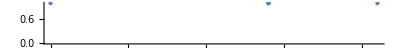

```mathematica
NumberLinePlot[MoonRadiuses]
```

The value at the left is the polar radius, the value in the middle is the average radius and the equatorial radius along orbit and the equatorial radius toward planet and the value at the right is the equatorial radius.

```mathematica
InputForm[Values[MoonRadiuses]]
```

{Quantity[1738.1`5., "Kilometers"], Quantity[1737.4`5., "Kilometers"], Quantity[1737.4`5., "Kilometers"], Quantity[1736.`5., "Kilometers"], 
 Quantity[1737.4`5., "Kilometers"]}

```mathematica
InputForm[MoonRadiuses]
```

<|EntityProperty["PlanetaryMoon", "EquatorialRadius"] -> Quantity[1738.1`5., "Kilometers"], 
 EntityProperty["PlanetaryMoon", "EquatorialRadiusAlongOrbit"] -> Quantity[1737.4`5., "Kilometers"], 
 EntityProperty["PlanetaryMoon", "EquatorialRadiusTowardPlanet"] -> Quantity[1737.4`5., "Kilometers"], 
 EntityProperty["PlanetaryMoon", "PolarRadius"] -> Quantity[1736.`5., "Kilometers"], 
 EntityProperty["PlanetaryMoon", "Radius"] -> Quantity[1737.4`5., "Kilometers"]|>

I wonder if there duplicates.

```mathematica
DuplicateFreeQ[MoonRadiuses]
```

False

These are the duplicates:

```mathematica
Complement[MoonRadiuses,DeleteDuplicates[MoonRadiuses]]
```

<|equatorial radius toward planet→1737.4 km,average radius→1737.4 km|>

I will solve the problem for each moon radius.

```mathematica
AssociationMap[FormulaData][FormulaLookup["Orbit"]]
```

<|EarthCircularOrbitPeriod→T Period==2 π √((1 /(M_♁ G)) ( a+h Height)^3),EllipticOrbitFormula→{A Length==a Length (1+e MultiplicativeConstants),P Length==a Length (1-e MultiplicativeConstants)},{CentripetalAcceleration,OrbitSpeed}→a Acceleration==(v Speed)^2/(d_o Distance),{CircularOrbitInMagneticField,Momentum}→r Radius==(p Momentum)/(B MagneticFluxDensity q ElectricCharge),{CircularOrbitInMagneticField,Speed}→r Radius==(m Mass v Speed)/(B MagneticFluxDensity q ElectricCharge),{CircularOrbitSpeed,Altitude}→v_c Speed==√((( G) m Mass)/(h Height+r_cb Radius)),{CircularOrbitSpeed,OrbitRadius}→v_c Speed==√((( G) m Mass)/(r Length)),{AngularToLinearVelocity,AngularVelocity,OrbitDistance}→v LinearSpeed==ω AngularVelocity d_o Distance,{AngularToLinearVelocity,Period,OrbitDistance}→v LinearSpeed==(2 π d_o Distance)/(T Period),{AngularToLinearVelocity,RotationRate,OrbitDistance}→v LinearSpeed==(2 π /rev) n RevolutionRate d_o Distance,{CentripetalAcceleration,AngularVelocity,OrbitDistance}→a Acceleration==(ω AngularVelocity)^2 d_o Distance,{CentripetalAcceleration,OrbitSpeed,Diameter}→a Acceleration==(2 (v Speed)^2)/(d Diameter),{CentripetalAcceleration,OrbitSpeed,Radius}→a Acceleration==(v Speed)^2/(r Radius),{CentripetalAcceleration,RotationRate,OrbitDistance}→a Acceleration==(4 π^2 /rev^2) (n RevolutionRate)^2 d_o Distance,{CentripetalAcceleration,RotationSpeed,OrbitDistance}→a Acceleration==(v Speed)^2/(d_o Distance),{HohmannTransferTime,OrbitalRadii,GravitationalParameter}→t_H Time==(π √((r_1 Length+r_2 Length)^3/(μ StandardGravitationalParameter)))/(2 √2),{HohmannTransferTime,OrbitalRadii,Mass}→t_H Time==(π √(((1 /G) (r_1 Length+r_2 Length)^3)/(M Mass)))/(2 √2)|>

I can generalize the first formula to the moon.

```mathematica
Take[AssociationMap[FormulaData][FormulaLookup["Orbit"]],1]
```

<|EarthCircularOrbitPeriod→T Period==2 π √((1 /(M_♁ G)) ( a+h Height)^3)|>

```mathematica
FormulaData["EarthCircularOrbitPeriod"]
```

T Period==2 π √((1 /(M_♁ G)) ( a+h Height)^3)

```mathematica
FullForm[FormulaData["EarthCircularOrbitPeriod"]]
```

Equal[QuantityVariable["T","Period"],Times[2,Pi,Power[Times[Quantity[1,Times[Power["EarthMass",-1],Power["GravitationalConstant",-1]]],Power[Plus[Quantity[None,"EarthEquatorialRadius"],QuantityVariable["h","Height"]],3]],Rational[1,2]]]]

```mathematica
InputForm[FormulaData["EarthCircularOrbitPeriod"]]
```

QuantityVariable["T", "Period"] == 2*Pi*Sqrt[Quantity[1, 1/("EarthMass"*"GravitationalConstant")]*
    (Quantity[None, "EarthEquatorialRadius"] + QuantityVariable["h", "Height"])^3]

```mathematica
FormulaData["EarthCircularOrbitPeriod"]/.<|Quantity["EarthMass"]->EntityValue[Entity["PlanetaryMoon","Moon"],EntityProperty["PlanetaryMoon","Mass"]]|>
```

T Period==2 π √((1 /(M_♁ G)) ( a+h Height)^3)

```mathematica
Replace[FormulaData["EarthCircularOrbitPeriod"],<|Quantity["EarthMass"]->EntityValue[Entity["PlanetaryMoon","Moon"],EntityProperty["PlanetaryMoon","Mass"]]|>,Infinity]
```

T Period==2 π √((1 /(M_♁ G)) ( a+h Height)^3)

```mathematica
ExpressionTree[FormulaData["EarthCircularOrbitPeriod"]]
```

-Graphics-

```mathematica
FormulaData["EarthCircularOrbitPeriod"]
```

T Period==2 π √((1 /(M_♁ G)) ( a+h Height)^3)

```mathematica
UnitDimensions[Quantity[, "GravitationalConstant"]]
```

{{LengthUnit,3},{MassUnit,-1},{TimeUnit,-2}}

```mathematica
QuantityVariable["G",UnitDimensions[Quantity[, "GravitationalConstant"]]]
```

QuantityVariable[G,UnitDimensions[ G]]

```mathematica
QuantityVariable["G",{{"LengthUnit",3},{"MassUnit",-1},{"TimeUnit",-2}}]
```

G {{LengthUnit,3},{MassUnit,-1},{TimeUnit,-2}}

```mathematica
QuantityVariable["G",Evaluate@UnitDimensions[Quantity[, "GravitationalConstant"]]]
```

G {{LengthUnit,3},{MassUnit,-1},{TimeUnit,-2}}

```mathematica
MoonCircularOrbitPeriod="T" "Period"==2 π Sqrt[(1/("M" "Mass" QuantityVariable["G",Evaluate@UnitDimensions[Quantity[, "GravitationalConstant"]]]))("r" "Radius"+"h" "Height")^3]
```

T Period==2 π √((h Height+r Radius)^3/(G {{LengthUnit,3},{MassUnit,-1},{TimeUnit,-2}} M Mass))

```mathematica
rules=moonRadius↦<|"G" {{"LengthUnit",3},{"MassUnit",-1},{"TimeUnit",-2}}->EntityValue[Entity["PhysicalConstant","GravitationalConstant"],EntityProperty["PhysicalConstant","Value"]],"h" "Height"->Quantity[95, "Kilometers"],"r" "Radius"->moonRadius,"M" "Mass"->EntityValue[Entity["PlanetaryMoon","Moon"],EntityProperty["PlanetaryMoon","Mass"]]|>
```

Function[moonRadius,Association[G {{LengthUnit,3},{MassUnit,-1},{TimeUnit,-2}}→EntityValue[gravitational constant,value],h Height→95 km,r Radius→moonRadius,M Mass→EntityValue[Moon,mass]]]

```mathematica
Map[moonRadius↦MoonCircularOrbitPeriod/.rules[moonRadius]][MoonRadiuses]
```

<|equatorial radius→T Period==7043. s,equatorial radius along orbit→T Period==7039. s,equatorial radius toward planet→T Period==7039. s,polar radius→T Period==7031. s,average radius→T Period==7039. s|>

```mathematica
MoonRadiuses
```

<|equatorial radius→1738.1 km,equatorial radius along orbit→1737.4 km,equatorial radius toward planet→1737.4 km,polar radius→1736. km,average radius→1737.4 km|>

```mathematica
Map[moonRadius↦{moonRadius,MoonCircularOrbitPeriod/.rules[moonRadius]}][MoonRadiuses]
```

<|equatorial radius→{1738.1 km,T Period==7043. s},equatorial radius along orbit→{1737.4 km,T Period==7039. s},equatorial radius toward planet→{1737.4 km,T Period==7039. s},polar radius→{1736. km,T Period==7031. s},average radius→{1737.4 km,T Period==7039. s}|>

```mathematica
Map[moonRadius↦{moonRadius,ReplaceAll[x_?QuantityQ->UnitConvert[x,"Kiloseconds"]][MoonCircularOrbitPeriod/.rules[moonRadius]]}][MoonRadiuses]
```

<|equatorial radius→{1738.1 km,T Period==7.043 ks},equatorial radius along orbit→{1737.4 km,T Period==7.039 ks},equatorial radius toward planet→{1737.4 km,T Period==7.039 ks},polar radius→{1736. km,T Period==7.031 ks},average radius→{1737.4 km,T Period==7.039 ks}|>

```mathematica
Map[moonRadius↦Cases[x_?QuantityQ][ReplaceAll[x_?QuantityQ->UnitConvert[x,"Kiloseconds"]][MoonCircularOrbitPeriod/.rules[moonRadius]]]][MoonRadiuses]
```

<|equatorial radius→{7.043 ks},equatorial radius along orbit→{7.039 ks},equatorial radius toward planet→{7.039 ks},polar radius→{7.031 ks},average radius→{7.039 ks}|>

```mathematica
Dataset[Map[moonRadius↦Cases[x_?QuantityQ][ReplaceAll[x_?QuantityQ->UnitConvert[x,"Kiloseconds"]][MoonCircularOrbitPeriod/.rules[moonRadius]]]][MoonRadiuses]]
```

The book has an answer of 7.05*10^3 s, which would be 7.05 ks. I think the difference is that I used more exact numbers.

```mathematica
WordDefinition["cord"]
```

{a line made of twisted fibers or threads,a cut pile fabric with vertical ribs; usually made of cotton,a light insulated conductor for household use,a unit of amount of wood cut for burning; 128 cubic feet,bind or tie with a cord,stack in cords}

```mathematica
WordDefinition["chord"]
```

{a combination of three or more notes that blend harmoniously when sounded together,a straight line connecting two points on a curve,bring into consonance, harmony, or accord while making music or singing,play chords on (a string instrument)}